#### gr. 1

Zad. 1

(-1+2 x)^4 (2+3 x)^2

2 (-1+2 x)^3 (2+3 x) (5+18 x)

{{x→-2/3},{x→-5/18},{x→1/2},{x→1/2},{x→1/2}}

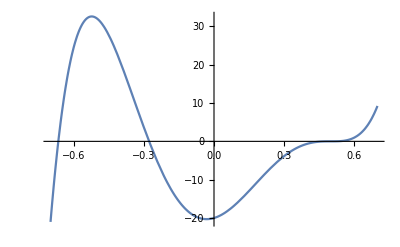

```mathematica
(2x-1)^4(3x+2)^2
D[%,x]//Factor
Solve[%==0,x]
Plot[%%,{x,-0.7,0.7}]
```

Zad. 2

```mathematica
(* (a) *)
```

```mathematica
L=(x+2)^2(x^2-3)//Expand;
M=(x+2)^2(3x+8)//Expand;
Limit[L/M,x->-2]
(* (b)  calka od 0 do 2 *)
f[x_]:=x^2+2x;
a1=f[0];
b1=f[1/2];
c1=f[1];
ml=f[0]/2+f[1/2]/2
mr=f[1/2]/2+f[1]/2
```

1/2

5/8

17/8

Zad. 3

```mathematica
Integrate[x^5+1/Cos[x]^2-5/((x^4)^(1/3)),x]
Integrate[(2x-1)/Sqrt[x^2-x+3],x]
Integrate[x Cos[5x],x]
```

x^6/6+(15 x)/((x^4)^(1/3))+Tan[x]

2 √(3-x+x^2)

1/25 Cos[5 x]+1/5 x Sin[5 x]

#### gr. 2

Zad. 1

48 x+12 x^2-16 x^3+3 x^4

48+24 x-48 x^2+12 x^3

{{x→2},{x→1-√3},{x→1+√3}}

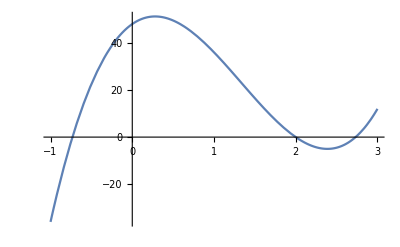

```mathematica
(x-2)(x-1-Sqrt[3])(x-1+Sqrt[3])//Expand;
Integrate[%,x] 12//Expand
D[%,x]
Solve[%==0,x]
Plot[%%,{x,-1,3}]
```

Zad. 2

```mathematica
(* (a) *)
```

```mathematica
L=Expand[x Sin[2x]];
M=Expand[1-Cos[3x]];
Limit[L/M,x->0]
L/M
(* (b) *)
f[x_]:=1-x^2;
a1=f[0];
b1=f[1/2];
c1=f[1];
mL=(f[0]+f[1/2])/2
mR=(f[1/2]+f[1])/2
```

4/9

(x Sin[2 x])/(1-Cos[3 x])

7/8

3/8

Zad. 3

```mathematica
Integrate[10/x^11-1/Sin[x]^2,x]
Integrate[1/(ArcSin[x]Sqrt[1-x^2]),x]
Integrate[x^(1/3)Log[x],x]
```

-1/x^10+Cot[x]

Log[ArcSin[x]]

3/16 x^(4/3) (-3+4 Log[x])